36

{4.03544,17.2659,16.7189,7.16701,3.09842,7.98772,11.0602,17.1931,5.56604,11.6999,16.1662,24.5223,22.8937,23.4706,13.9753,16.2153,11.383,19.799,31.2681,22.2778,32.0341,19.5593,21.4763,21.6497,21.6404,20.8311,24.2438,15.0484,16.3622,18.3175,30.7133,23.8137,22.2146,30.7601,23.0913,23.7134}

14400.

14400.

{74,2}

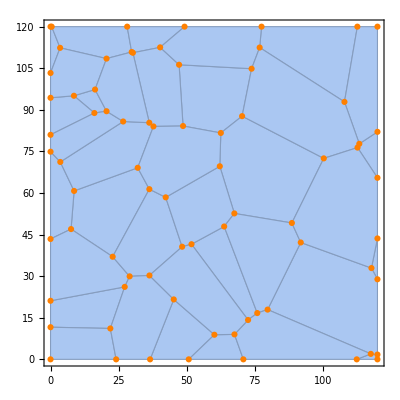

```mathematica
SeedRandom["LookAtThisSeed"]
xmin=-20;xmax=140;temp=20;
pts=RandomReal[{xmin,xmax},{40,2}];
mesh=VoronoiMesh[pts,{{xmin+temp,xmax-temp},{xmin+temp,xmax-temp}}];
grid=MeshPrimitives[mesh,2];
dim=Dimensions[grid][[1]]
Table[Sqrt[Area[grid[[i]]]],{i,dim}]
Sum[Area[grid[[i]]],{i,dim}]
Area[mesh]
vertices=MeshCoordinates[mesh];
vertices1=Dimensions[vertices]
ptsLabels=Text[#,pts[[#]],{-2,0}]&/@Range[Length@pts];
meshLabels=Text[#+Length@pts,MeshCoordinates[mesh][[#]],{-2,0}]&/@Range[Length@MeshCoordinates[mesh]];

Show[mesh,(*ListPlot[pts,PlotStyle->Red],Graphics[{Red,ptsLabels}],*)ListPlot[vertices,PlotStyle->Orange],Frame->True,AspectRatio->1(*,Graphics[{Red,meshLabels}]*)]
```

4

{14.2734,24.284,21.2349,18.8584}

1600.

1600.

{10,2}

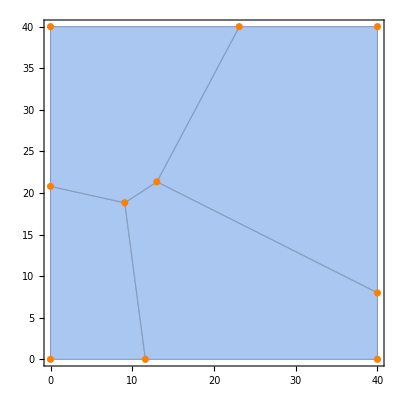

```mathematica
SeedRandom["LookAtThisSeed"]
xmin=-10.;xmax=50.;temp=10.;
pts=RandomReal[{xmin,xmax},{4,2}];
mesh=VoronoiMesh[pts,{{xmin+temp,xmax-temp},{xmin+temp,xmax-temp}}];
grid=MeshPrimitives[mesh,2];
dim=Dimensions[grid][[1]]
Table[Sqrt[Area[grid[[i]]]],{i,dim}]
Sum[Area[grid[[i]]],{i,dim}]
Area[mesh]
vertices=MeshCoordinates[mesh];
vertices1=Dimensions[vertices]
ptsLabels=Text[#,pts[[#]],{-2,0}]&/@Range[Length@pts];
meshLabels=Text[#+Length@pts,MeshCoordinates[mesh][[#]],{-2,0}]&/@Range[Length@MeshCoordinates[mesh]];

Show[mesh,(*ListPlot[pts,PlotStyle->Red],Graphics[{Red,ptsLabels}],*)ListPlot[vertices,PlotStyle->Orange],Frame->True,AspectRatio->1(*,Graphics[{Red,meshLabels}]*)]
```

```mathematica
dim2=Dimensions[MeshPrimitives[mesh,1]][[1]]
edges2=MeshPrimitives[mesh,1]/.Line[{a_,b_}]:>UndirectedEdge[a,b]
edges=Table[MeshPrimitives[mesh,1][[i,1]],{i,dim2}]
list2={xmin+temp,xmax-temp};
edges1=Table[list1=Flatten[edges[[i]]];
r=Fold[DeleteCases[#1,#2]&,list1,list2];If[Length[r]≥3,edges[[i]],Unevaluated[Sequence[]]],{i,dim2}]
```

13

{{11.6084,0.}<->{9.08334,18.8267},{9.08334,18.8267}<->{0.,20.7977},{0.,20.7977}<->{0.,0.},{0.,0.}<->{11.6084,0.},{23.0906,40.}<->{13.0111,21.3405},{13.0111,21.3405}<->{40.,7.99041},{40.,7.99041}<->{40.,40.},{40.,40.}<->{23.0906,40.},{40.,0.}<->{40.,7.99041},{13.0111,21.3405}<->{9.08334,18.8267},{11.6084,0.}<->{40.,0.},{0.,40.}<->{0.,20.7977},{23.0906,40.}<->{0.,40.}}

{{{11.6084,0.},{9.08334,18.8267}},{{9.08334,18.8267},{0.,20.7977}},{{0.,20.7977},{0.,0.}},{{0.,0.},{11.6084,0.}},{{23.0906,40.},{13.0111,21.3405}},{{13.0111,21.3405},{40.,7.99041}},{{40.,7.99041},{40.,40.}},{{40.,40.},{23.0906,40.}},{{40.,0.},{40.,7.99041}},{{13.0111,21.3405},{9.08334,18.8267}},{{11.6084,0.},{40.,0.}},{{0.,40.},{0.,20.7977}},{{23.0906,40.},{0.,40.}}}

{{{11.6084,0.},{9.08334,18.8267}},{{9.08334,18.8267},{0.,20.7977}},{{23.0906,40.},{13.0111,21.3405}},{{13.0111,21.3405},{40.,7.99041}},{{13.0111,21.3405},{9.08334,18.8267}}}

```mathematica
weights=edges2/.UndirectedEdge->EuclideanDistance
```

{18.9953,9.29472,20.7977,11.6084,21.2078,30.1103,32.0096,16.9094,7.99041,4.66331,28.3916,19.2023,23.0906}

```mathematica
MeshPrimitives[mesh,1][[1]]
Dimensions[MeshPrimitives[mesh,1]]
```

Line[{{11.6084,0.},{9.08334,18.8267}}]

{13}